```mathematica
SX[1]=JSX[6]Exp[-I kx]+JSX[2]+JSX[3];
SY[1]=JSY[6]Exp[-I kx]+JSY[2]+JSY[3];
SZ[1]=JSZ[6]Exp[-I kx]+JSZ[2]+JSZ[3];

SX[2]=JSX[1]+JSX[3];
SY[2]=JSY[1]+JSY[3];
SZ[2]=JSZ[1]+JSZ[3];

SX[3]=JSX[1]+JSX[2]+JSX[4];
SY[3]=JSY[1]+JSY[2]+JSY[4];
SZ[3]=JSZ[1]+JSZ[2]+JSZ[4];

SX[4]=JSX[3]+JSX[5]+JSX[6];
SY[4]=JSY[3]+JSY[5]+JSY[6];
SZ[4]=JSZ[3]+JSZ[5]+JSZ[6];

SX[5]=JSX[4]+JSX[6];
SY[5]=JSY[4]+JSY[6];
SZ[5]=JSZ[4]+JSZ[6];

SX[6]=JSX[4]+JSX[5]+JSX[1]Exp[I kx];
SY[6]=JSY[4]+JSY[5]+JSY[1]Exp[I kx];
SZ[6]=JSZ[4]+JSZ[5]+JSZ[1]Exp[I kx];

JMT= CoefficientArrays[Flatten[Table[{SX[i],SY[i],SZ[i]},{i,1,6}]]==0,Flatten[Table[{JSX[i],JSY[i],JSZ[i]},{i,1,6}]]][[2]];
Clear[HJ];
MatrixForm[JMT]
```

```mathematica
HJ[kx_]:=({{0, 0, 0, 1, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(-ⅈ kx), 0, 0}, {0, 0, 0, 0, 1, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(-ⅈ kx), 0}, {0, 0, 0, 0, 0, 1, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(-ⅈ kx)}, {1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1}, {ⅇ^(ⅈ kx), 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 1, 0, 0, 0, 0, 0}, {0, ⅇ^(ⅈ kx), 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 1, 0, 0, 0, 0}, {0, 0, ⅇ^(ⅈ kx), 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 1, 0, 0, 0}})
```

```mathematica
Eigensystem[HJ[Pi+0.0]]
```

{{2.21432,2.21432,2.21432,2.21432,2.21432,2.21432,-1.67513,-1.67513,-1.67513,-1.67513,-1.67513,-1.67513,-0.539189,-0.539189,-0.539189,-0.539189,-0.539189,-0.539189},{{0.221443+0.000727838 ⅈ,-0.0868758-0.113198 ⅈ,-0.117523-0.0957065 ⅈ,0.0630724+0.0290571 ⅈ,-0.117081-0.0987566 ⅈ,-0.117523-0.0957065 ⅈ,-0.0817809+0.0636139 ⅈ,-0.172378-0.105481 ⅈ,-0.142711-0.116218 ⅈ,-0.465605+0.111076 ⅈ,-0.177744-0.0216138 ⅈ,-0.080961-0.0659315 ⅈ,-0.440162+0.0912857 ⅈ,-0.124116+0.0112021 ⅈ,-0.0365625-0.029775 ⅈ,-0.509055+0.0910593 ⅈ,-0.0970882+0.0464189 ⅈ,0.},{0.124109-0.0468212 ⅈ,0.343672+0.198957 ⅈ,-0.233388-0.00778118 ⅈ,0.084968-0.0682497 ⅈ,0.325742+0.228143 ⅈ,-0.233388-0.00778118 ⅈ,0.0640371-0.104305 ⅈ,0.377624+0.306224 ⅈ,-0.283407-0.00944884 ⅈ,-0.0672787-0.115895 ⅈ,0.166766+0.250978 ⅈ,-0.160779-0.0053604 ⅈ,-0.0872012-0.0834445 ⅈ,0.0492846+0.155709 ⅈ,-0.0726087-0.00242079 ⅈ,-0.125813-0.068878 ⅈ,-0.0576346+0.093812 ⅈ,0.},{0.,0.,0.342485+4.19424×10^-17 ⅈ,0.,0.,0.154668+1.89414×10^-17 ⅈ,0.,0.,0.+1.89414×10^-17 ⅈ,0.,0.,-0.497154,0.,0.,-0.497154,0.,0.,-0.603704},{0.0611745+0.0401952 ⅈ,-0.297997-0.0129235 ⅈ,-0.0499958-0.16949 ⅈ,0.0456988+0.038124 ⅈ,-0.124342-0.00822704 ⅈ,-0.0499958-0.16949 ⅈ,0.0400173+0.0442236 ⅈ,0.0226631-0.00529384 ⅈ,-0.0607109-0.205816 ⅈ,-0.0182623+0.019606 ⅈ,0.472523+0.00942823 ⅈ,-0.0344417-0.116761 ⅈ,-0.030712+0.00584772 ⅈ,0.465472+0.0110752 ⅈ,-0.0155541-0.0527298 ⅈ,-0.0497438-0.00665731 ⅈ,0.558182+0.0150958 ⅈ,0.},{0.341786+0.3257 ⅈ,0.164465-0.103385 ⅈ,0.0149777-0.0469117 ⅈ,0.337368+0.323218 ⅈ,0.137384-0.105769 ⅈ,0.0149777-0.0469117 ⅈ,0.405255+0.390007 ⅈ,0.139747-0.130822 ⅈ,0.0181877-0.0569658 ⅈ,0.21821+0.214682 ⅈ,0.00759488-0.0805284 ⅈ,0.010318-0.0323171 ⅈ,0.0921323+0.093348 ⅈ,-0.0358814-0.0398286 ⅈ,0.00465969-0.0145946 ⅈ,-0.0141999-0.00797988 ⅈ,-0.0870477-0.00766483 ⅈ,0.},{-0.159816+0.209827 ⅈ,-0.145894-0.195986 ⅈ,-0.359486+0.0823307 ⅈ,-0.100117+0.150106 ⅈ,-0.145633-0.150557 ⅈ,-0.359486+0.0823307 ⅈ,-0.0618747+0.122556 ⅈ,-0.176584-0.137395 ⅈ,-0.436531+0.0999758 ⅈ,0.122923-0.0885552 ⅈ,-0.0994862+0.0423077 ⅈ,-0.247647+0.056717 ⅈ,0.142172-0.126683 ⅈ,-0.0445497+0.0850522 ⅈ,-0.111839+0.0256137 ⅈ,0.191892-0.191962 ⅈ,0.000839062+0.146025 ⅈ,0.},{0.0981602-0.0512719 ⅈ,0.406049+0.21969 ⅈ,-0.0496595+0.116378 ⅈ,-0.0260355+0.0305569 ⅈ,-0.282665-0.143123 ⅈ,-0.0496595+0.116378 ⅈ,-0.0545473+0.0000851514 ⅈ,0.0674516+0.0200607 ⅈ,0.132846-0.311325 ⅈ,0.0192492+0.0205724 ⅈ,-0.236374-0.110171 ⅈ,-0.123215+0.288755 ⅈ,-0.061546+0.0206985 ⅈ,-0.136465-0.0804568 ⅈ,0.0735554-0.172378 ⅈ,0.0838483-0.0552451 ⅈ,0.464972+0.244946 ⅈ,0.},{-0.0457298-0.193448 ⅈ,0.2485+0.0119655 ⅈ,-0.0152009+0.00989385 ⅈ,-0.101097+0.0238395 ⅈ,0.184784-0.0137652 ⅈ,-0.0152009+0.00989385 ⅈ,0.215081+0.153513 ⅈ,-0.558038+0.011093 ⅈ,0.0406645-0.0264673 ⅈ,-0.213461-0.0875467 ⅈ,0.501502-0.0167825 ⅈ,-0.0377165+0.0245486 ⅈ,0.105115+0.139836 ⅈ,-0.32506-0.000351633 ⅈ,0.0225155-0.0146547 ⅈ,0.0373802-0.146697 ⅈ,0.0430162+0.0173715 ⅈ,0.},{-0.170321+0.373025 ⅈ,0.137227+0.0482487 ⅈ,0.0236835+0.0314488 ⅈ,0.28194-0.13545 ⅈ,0.0757686-0.00927871 ⅈ,0.0236835+0.0314488 ⅈ,-0.301966-0.146128 ⅈ,-0.264149-0.0327057 ⅈ,-0.0633565-0.0841295 ⅈ,0.394213+0.0072085 ⅈ,0.229489+0.0158163 ⅈ,0.0587634+0.0780305 ⅈ,-0.0530573-0.209235 ⅈ,-0.161767-0.0326272 ⅈ,-0.0350799-0.0465817 ⅈ,-0.305335+0.343287 ⅈ,0.0414925+0.0388386 ⅈ,0.},{0.,0.,0.593007+7.26224×10^-17 ⅈ,0.,0.,-0.354007-4.33533×10^-17 ⅈ,0.,0.,0.-4.33533×10^-17 ⅈ,0.,0.,-0.239001,0.,0.,-0.239001,0.,1.11022×10^-16,0.639358},{0.107395-0.0000711326 ⅈ,-0.321903+0.00457066 ⅈ,0.0300419+0.193644 ⅈ,-0.0631135+0.000159637 ⅈ,0.192674-0.00290512 ⅈ,0.0300419+0.193644 ⅈ,-0.00167179-0.00019628 ⅈ,-0.000849971+0.0002958 ⅈ,-0.0803661-0.518023 ⅈ,-0.0414812+0.000240291 ⅈ,0.130654-0.00216104 ⅈ,0.0745399+0.480468 ⅈ,-0.0439575-0.0000504385 ⅈ,0.129395-0.0017229 ⅈ,-0.044498-0.286824 ⅈ,0.115116-0.0001558 ⅈ,-0.347407+0.00504713 ⅈ,0.},{0.101394-0.408694 ⅈ,-0.0570692-0.0754036 ⅈ,-0.027214-0.00956627 ⅈ,0.208161+0.157766 ⅈ,0.0566403-0.039458 ⅈ,-0.027214-0.00956627 ⅈ,-0.450091+0.144416 ⅈ,-0.0378107+0.141501 ⅈ,0.072801+0.025591 ⅈ,0.444406+0.00901308 ⅈ,0.0637668-0.122171 ⅈ,-0.0675232-0.0237358 ⅈ,-0.222266+0.222921 ⅈ,0.00776179+0.0874194 ⅈ,0.0403092+0.0141695 ⅈ,-0.0720817-0.382434 ⅈ,-0.0767688-0.0242679 ⅈ,0.},{-0.306603+0.102552 ⅈ,0.0491478+0.107829 ⅈ,-0.0636052+0.121333 ⅈ,0.128633+0.233096 ⅈ,-0.0128022+0.107467 ⅈ,-0.0636052+0.121333 ⅈ,0.237246-0.228235 ⅈ,-0.042245-0.165774 ⅈ,0.0979005-0.186755 ⅈ,0.0500502-0.212587 ⅈ,-0.0135675-0.125912 ⅈ,0.0744236-0.14197 ⅈ,-0.464794+0.282703 ⅈ,0.0781077+0.233832 ⅈ,-0.138029+0.263303 ⅈ,0.200562+0.0601564 ⅈ,-0.0285472-0.000167127 ⅈ,0.},{-0.271409+0.00913192 ⅈ,0.143729-0.11189 ⅈ,0.00511199-0.0379322 ⅈ,0.147343-0.353936 ⅈ,0.164303-0.134597 ⅈ,0.00511199-0.0379322 ⅈ,0.191963+0.181706 ⅈ,-0.23232+0.184463 ⅈ,-0.00786832+0.0583848 ⅈ,0.0205612+0.24683 ⅈ,-0.182768+0.147026 ⅈ,-0.00598147+0.0443839 ⅈ,-0.396015-0.147489 ⅈ,0.321386-0.253274 ⅈ,0.0110935-0.0823161 ⅈ,0.192966-0.167306 ⅈ,0.0094804-0.0104637 ⅈ,0.},{-0.0983779+0.160474 ⅈ,-0.142726+0.102442 ⅈ,-0.113089-0.114169 ⅈ,0.422803-0.280331 ⅈ,-0.0884099+0.00239201 ⅈ,-0.113089-0.114169 ⅈ,-0.129593-0.00932228 ⅈ,0.190395-0.103731 ⅈ,0.174065+0.175727 ⅈ,-0.25455+0.124884 ⅈ,0.128477-0.0489029 ⅈ,0.132324+0.133587 ⅈ,0.0266772+0.145114 ⅈ,-0.284698+0.176203 ⅈ,-0.245412-0.247756 ⅈ,0.240166-0.203128 ⅈ,0.0250293-0.046104 ⅈ,0.},{0.110571-0.0273746 ⅈ,0.134384-0.0727827 ⅈ,-0.214986-0.0317952 ⅈ,0.048913+0.261098 ⅈ,0.0989051-0.171026 ⅈ,-0.214986-0.0317952 ⅈ,-0.136944-0.113407 ⅈ,-0.187713+0.164998 ⅈ,0.330905+0.0489389 ⅈ,-0.085645-0.172576 ⅈ,-0.132077+0.154844 ⅈ,0.251553+0.0372032 ⅈ,0.211536+0.0735262 ⅈ,0.275276-0.203216 ⅈ,-0.466539-0.0689984 ⅈ,-0.0284126+0.132931 ⅈ,-0.0163491-0.0452718 ⅈ,0.},{0.,0.,0.362003+4.43326×10^-17 ⅈ,0.,0.,-0.671384-8.22209×10^-17 ⅈ,0.,0.,0.-8.22209×10^-17 ⅈ,0.,0.,0.309381,0.,0.,0.309381,0.,2.22045×10^-16,-0.476196},{0.00928825+0.00168739 ⅈ,-0.354007-0.000914256 ⅈ,-0.0204415+0.044866 ⅈ,-0.0261374-0.00417387 ⅈ,0.665425-0.00214786 ⅈ,-0.0204415+0.044866 ⅈ,0.00480477+0.000563112 ⅈ,-0.00478313+0.00207236 ⅈ,0.0314634-0.0690573 ⅈ,0.0142585+0.00218285 ⅈ,-0.308839+0.00194472 ⅈ,0.0239184-0.0524971 ⅈ,0.00383175+0.000960851 ⅈ,-0.29846-0.00255247 ⅈ,-0.0443599+0.0973632 ⅈ,-0.0163246-0.00270093 ⅈ,0.469765-0.000568457 ⅈ,0.}}}

```mathematica
EJ[kx_]:=Sort[Re[Eigenvalues[HJ[kx]]]];
```

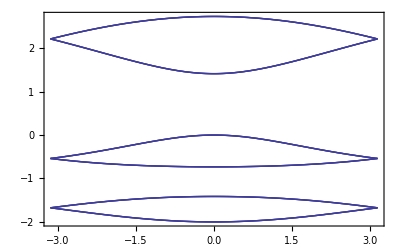

```mathematica
Plot[EJ[kx],{kx,-Pi,Pi},Frame->True]
```